# COMPLEX ANALYSIS

## Submitted By: Ayushi Singh Course: BSc(hons.) Mathematics Roll no:23563/8 Submitted to:Mr. Ankit Gupta

01

GEOMETRIC PLOT nth ROOTS OF UNITY

## Make a geometric plot to show that the roots of unity are equally spaced points that lie on the unit circle C_{1}(0)={z:|z|=1} and form the vertices of a regular polygon with n sides , for n=4,5,6,7,8.

a) For n=4

Here we have to find roots for z^4=1

```mathematica
Sol=ComplexExpand[z/.N[Solve[z^4==1]]]
```

{-1.,0.-1. ⅈ,0.+1. ⅈ,1.}

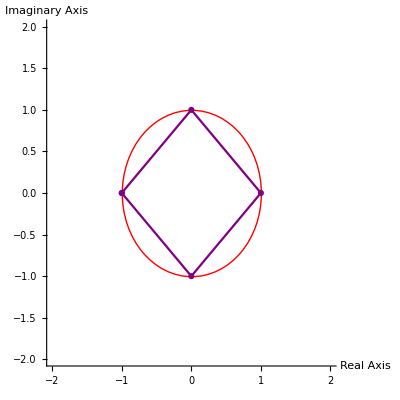

{{z→-2 ⅈ},{z→ⅈ+√3},{z→ⅈ-√3}}

{-2 ⅈ,ⅈ+√3,ⅈ-√3}

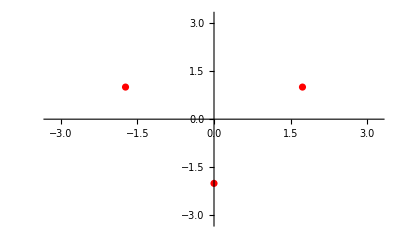

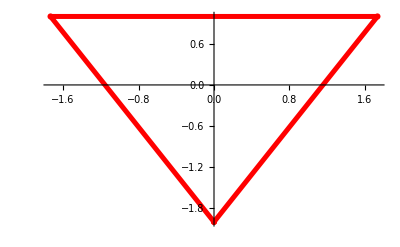

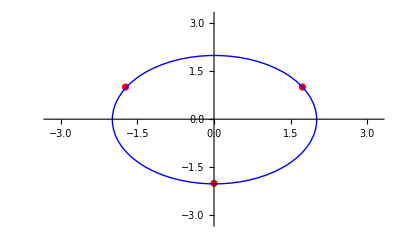

```mathematica
Show[Graphics[{Thick,Red,Circle[{0,0},1]}],
ListLinePlot[{{-1,0},{0,1},{1,0},{0,-1},{-1,0}},
PlotStyle->Purple,PlotMarkers->Automatic],Axes->True,
PlotRange->{{-2,2},{-2,2}},AxesLabel->{"Real Axis","Imaginary Axis"}]
```

b) For n=5

Here we have to find roots for z^5=1

```mathematica
Sol=ComplexExpand[z/.N[Solve[z^5==1]]]
```

{1.,-0.809017-0.587785 ⅈ,0.309017+0.951057 ⅈ,0.309017-0.951057 ⅈ,-0.809017+0.587785 ⅈ}

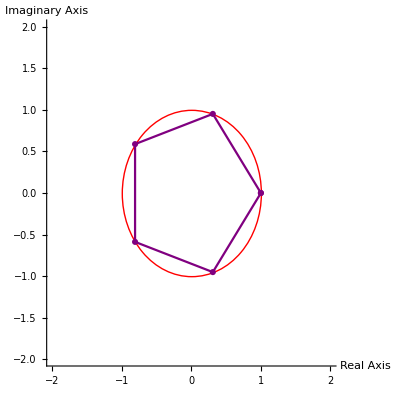

```mathematica
Show[Graphics[{Thick,Red,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1,0}},
PlotStyle->Purple,PlotMarkers->Automatic],Axes->True,
PlotRange->{{-2,2},{-2,2}},AxesLabel->{"Real Axis","Imaginary Axis"}]
```

c) For n=6

Here we have to find roots for z^6=1

```mathematica
Sol=ComplexExpand[z/.N[Solve[z^6==1]]]
```

{-1.,1.,-0.5-0.866025 ⅈ,0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ}

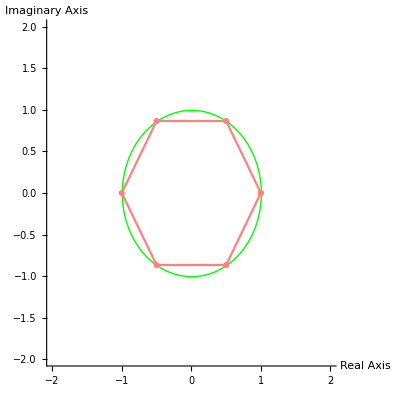

```mathematica
Show[Graphics[{Thick,Green,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.5,0.866025},{-0.5,0.866025},{-1,0},{-0.5,-0.866025},{0.5,-0.866025},{1,0}},
PlotStyle->Pink,PlotMarkers->Automatic],Axes->True,
PlotRange->{{-2,2},{-2,2}},AxesLabel->{"Real Axis","Imaginary Axis"}]
```

d) For n=7

Here we have to find roots for z^7=1

```mathematica
Sol=ComplexExpand[z/.N[Solve[z^7==1]]]
```

{1.,-0.900969-0.433884 ⅈ,0.62349+0.781831 ⅈ,-0.222521-0.974928 ⅈ,-0.222521+0.974928 ⅈ,0.62349-0.781831 ⅈ,-0.900969+0.433884 ⅈ}

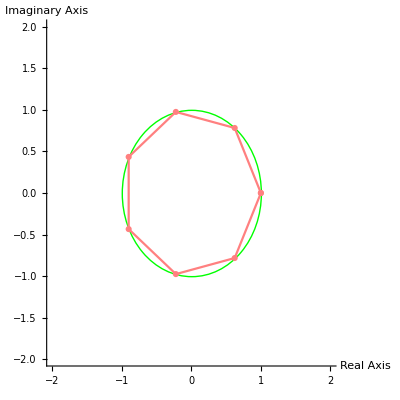

```mathematica
Show[Graphics[{Thick,Green,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.62349,0.781831},{-0.222521,0.974928},{-0.900969,0.433884},{-0.900969,-0.433884},{-0.222521,-0.974928},{0.62349,-0.781831},{1,0}},
PlotStyle->Pink,PlotMarkers->Automatic],Axes->True,
PlotRange->{{-2,2},{-2,2}},AxesLabel->{"Real Axis","Imaginary Axis"}]
```

e) For n=8

Here we have to find roots for z^8=1

```mathematica
Sol=ComplexExpand[z/.N[Solve[z^8==1]]]
```

{-1.,0.-1. ⅈ,0.+1. ⅈ,1.,-0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,-0.707107+0.707107 ⅈ}

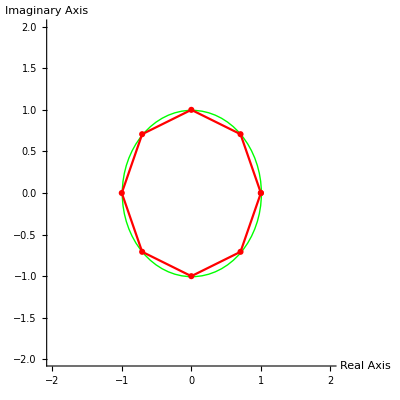

```mathematica
Show[Graphics[{Thick,Green,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.707107,0.707107},{0,1},{-0.707107,0.707107},{-1,0},{-0.707107,-0.707107},{0,-1},{0.707107,-0.707107},{1,0}},
PlotStyle->Red,PlotMarkers->Automatic],Axes->True,
PlotRange->{{-2,2},{-2,2}},AxesLabel->{"Real Axis","Imaginary Axis"}]
```

02

PLOTTING SOLUTIONS OF z^3=8i

## Find all the solutions of the equation z^3=8i and represent these geometrically

```mathematica
Sol1=ComplexExpand[Solve[z^3-8 I==0]]
z/.Sol1
```

{{z→-2 ⅈ},{z→ⅈ+√3},{z→ⅈ-√3}}

{-2 ⅈ,ⅈ+√3,ⅈ-√3}

```mathematica
rootplot=ListPlot[{Re[z],Im[z]}/.Sol1,
PlotRange->{{-3.2,3.2},{-3.2,3.2}},PlotStyle->{Red}]
```

-Graphics-

```mathematica
ListLinePlot[{{0,-2},{Sqrt[3],1},{-Sqrt[3],1},{0,-2}},
PlotStyle->{Red,Thickness->0.009},PlotMarkers->Automatic]
```

-Graphics-

```mathematica
Show[rootplot,Graphics[{Blue,Circle[{0,0},2]}]]
```

-Graphics-

03

PLOTTING SOME REGIONS (PARAMETRIC EQUATIONS)

## 1. Unit Disc

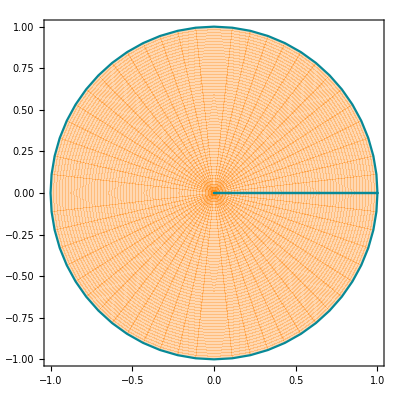

```mathematica
ParametricPlot[{r*Cos[t],r*Sin[t]},{r,0,1},{t,0,2 Pi},PlotStyle->{Thick,Orange}]
```

## 2. Ellipse centered at origin with horizontal major axis of 4 units and vertical minor axis of 2 units.

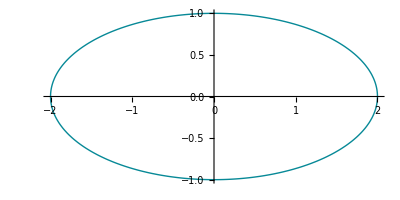

```mathematica
ParametricPlot[{2 Cos[t],1 Sin[t]},{t,0,2 Pi},PlotStyle->Thick]
```

## 3. Annulus - {z: 2 < |z| < 3}.

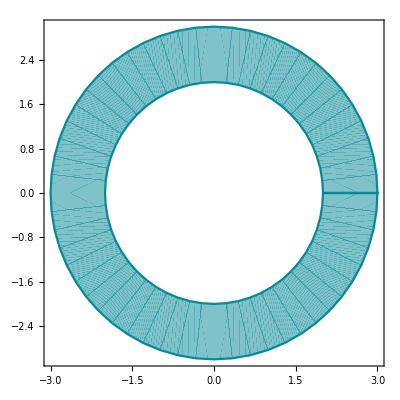

```mathematica
ParametricPlot[{r*Cos[t],r*Sin[t]},{r,2,3},{t,0,2Pi},PlotStyle->Thick]
```

## 4. Show the effect of rotation of the ellipse (Q2) by an angle of Π/6 radians and shifting of the centre from (0,0) to (2,1) by making a parametric plot.

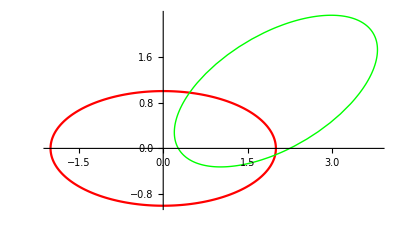

```mathematica
p1=ParametricPlot[{2*Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->Red];
f[q_]=q*Exp[I Pi/6]+2+I;
g[t_]=f[2 Cos[t]+I Sin[t]];
p2=ParametricPlot[{Re[g[t]],Im[g[t]]},{t,0,2 Pi},PlotStyle->{Thick,Green}];
Show[p1,p2,PlotRange->4]
```

## 5 Plot the image of S = {z: |z| < 1 and 0 <= Argz <= Pi/6} under the function f(z) = z^3.

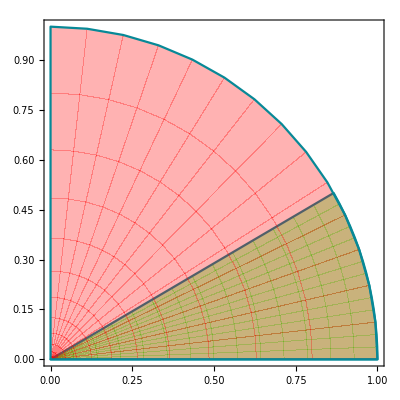

```mathematica
Clear[z]
f[z_]=z^3;
p3=ParametricPlot[{r Cos[t],r Sin[t]},{r,0,1},{t,0,Pi/6},PlotStyle->Green];
g[r_,t_]=f[r Exp[I t]];
p4=ParametricPlot[{Re[g[r,t]],Im[g[r,t]]},{r,0,1},{t,0,Pi/6},PlotStyle->Red];
Show[{p3,p4},PlotRange->1]
```

## 6. Plot the image of right branch of hyperbola x^2 - y^2= 1 under the function f(z) = z^2.

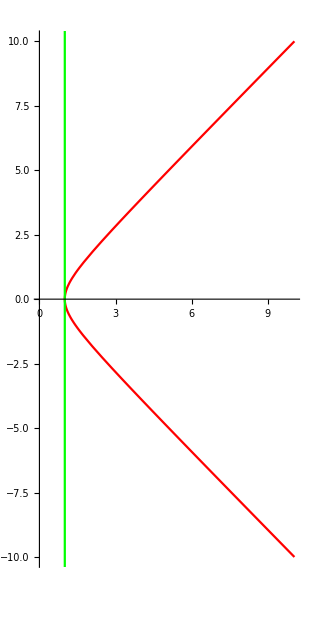

```mathematica
f[z_]=z^2;
p5=ParametricPlot[{(1+ y^2)^(1/2),y},{y,-10,10},AxesOrigin->{0,0},PlotStyle->Red];
g[x_,y_]=ComplexExpand[f[x+I*y]];
p6=ParametricPlot[{Re[g[(1+ y^2)^(1/2),y]],Im[g[(1+ y^2)^(1/2),y]]},{y,-10,10},AxesOrigin->{0,0},PlotStyle->Green];
Show[p5,p6]
```

## 7. Plot the image of line segment x = 1, -5 ≤ y ≤ 5 under the function f(z)= z^2.

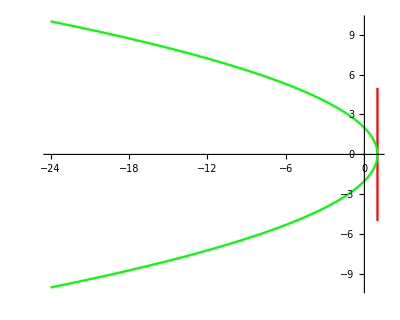

```mathematica
f[z_]=z^2;
g[x_,y_]=ComplexExpand[f[x+I*y]];
p7=ParametricPlot[{1,y},{y,-5,5},PlotStyle->Red];
p6=ParametricPlot[{Re[g[1,y]],Im[g[1,y]]},{y,-5,5},PlotStyle->Green];
Show[{p7,p6},PlotRange->5]
```

## 8.Plot the image of region bounded by lines x =1, x = 5, y=1, y=5 under the function f(z) = z2.

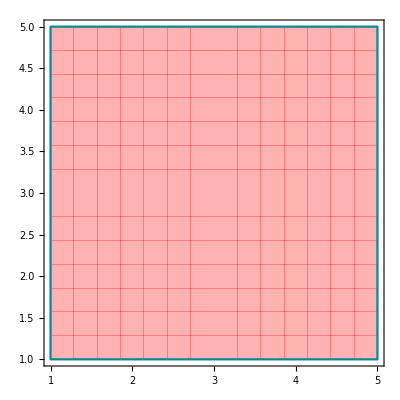

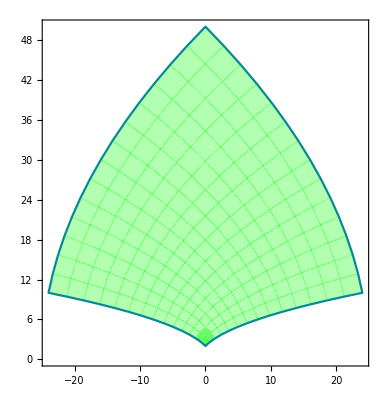

```mathematica
f[z_]=z^2;
g[x_,y_]=ComplexExpand[f[x+I*y]];
p7=ParametricPlot[{x,y},{x,1,5},{y,1,5},PlotStyle->Red]
p6=ParametricPlot[{Re[g[x,y]],Im[g[x,y]]},{x,1,5},{y,1,5},PlotStyle->Green]
```

## 9.Plot the image of vertical line segment x=1, -2<= y <=2 under the function f(z) = e^z

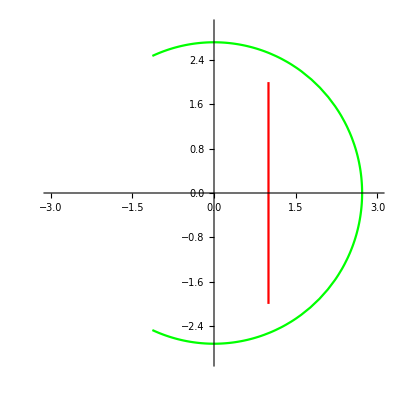

```mathematica
f[z_]=Exp[z];
g[x_,y_]=ComplexExpand[f[x+I*y]];
p1=ParametricPlot[{1,y},{y,-2,2},PlotStyle->Red];
p2=ParametricPlot[{Re[g[1,y]],Im[g[1,y]]},{y,-2,2},PlotStyle->Green];
Show[{p1,p2},PlotRange->{{-3,3},{-3,3}}]
```

## 10.Plot the image of vertical line segment y=1, -2<= x <=2 under the function f(z) = e^z

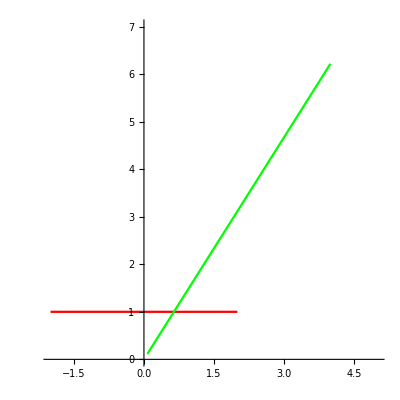

```mathematica
f[z_]=Exp[z];
g[x_,y_]=ComplexExpand[f[x+I*y]];
p1=ParametricPlot[{x,1},{x,-2,2},PlotStyle->Red];
p2=ParametricPlot[{Re[g[x,1]],Im[g[x,1]]},{x,-2,2},PlotStyle->Green];
Show[{p1,p2},PlotRange->{{-2,5},{0,7}}]
```

## 11.Plot the image of region bounded by lines x=1, x=3, y=1, y=3 under exponential function

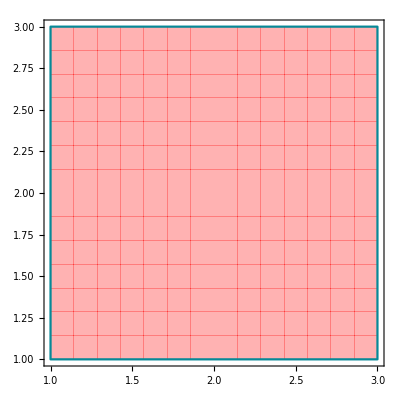

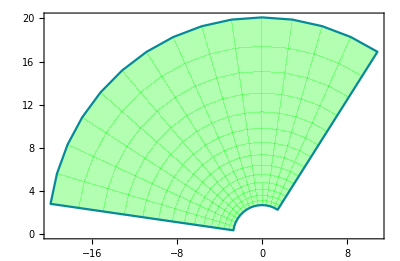

```mathematica
f[z_]=Exp[z];
g[x_,y_]=ComplexExpand[f[x+I*y]];
p1=ParametricPlot[{x,y},{x,1,3},{y,1,3},PlotStyle->Red]
p2=ParametricPlot[{Re[g[x,y]],Im[g[x,y]]},{x,1,3},{y,1,3},PlotStyle->Green]
```

## 13. Plot image of circle |z|=1 under the function f(z)=(1-z)/(1+z).

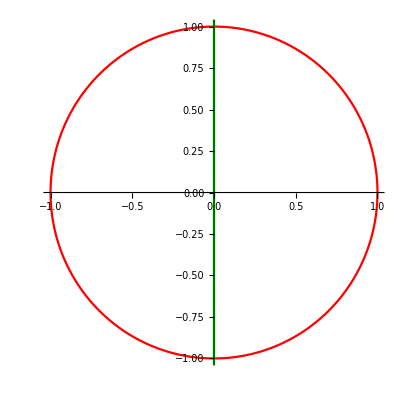

```mathematica
f[z_]=(1-z)/(1+z);
g[t_]=ComplexExpand[f[Exp[I*t]]];
p1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->Red];
p2=ParametricPlot[{Re[g[t]],Im[g[t]]},{t,0,2*Pi},PlotStyle->Green];
Show[p1,p2]
```

## 14. Plot image of circle |z|=1 under the function f(z)=(1-z)/(1+z).

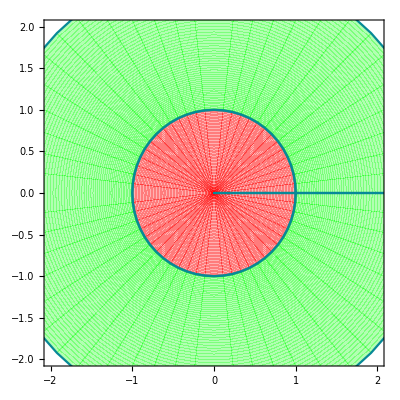

```mathematica
f[z_]=(1-z)/(1+z);
g[t_]=ComplexExpand[f[r Exp[I*t]]];
p1=ParametricPlot[{r Cos[t],r Sin[t]},{r,0,1},{t,0,2*Pi},PlotStyle->Red];
p2=ParametricPlot[{Re[g[r,t]],Im[g[r,t]]},{r,0,1},{t,0,2*Pi},PlotStyle->Green];
Show[{p1,p2},PlotRange->{{-2,2},{-2,2}}]
```

## 15. Plot image of circle |z|=1 under the function f(z)=(z-1)/(z+1).

```mathematica
f[z_]=(z-1)/(z+1);
g[t_]=ComplexExpand[f[Exp[I*t]]];
p1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->Red];
p2=ParametricPlot[{Re[g[t]],Im[g[t]]},{t,0,2*Pi},PlotStyle->Green];
Show[p1,p2]
```

-Graphics-

## 16. Plot image of circle |z|=1 under the function f(z)=(z-1)/(z+1).

```mathematica
f[z_]=(z-1)/(z+1);
g[t_]=ComplexExpand[f[r Exp[I*t]]];
p1=ParametricPlot[{r Cos[t],r Sin[t]},{r,0,1},{t,0,2*Pi},PlotStyle->Red];
p2=ParametricPlot[{Re[g[r,t]],Im[g[r,t]]},{r,0,1},{t,0,2*Pi},PlotStyle->{Thick,Green}];
Show[{p1,p2},PlotRange->{{-2,2},{-2,2}}]
```

-Graphics-

04

PLOTTING IMAGE OF DISK UNDER LINEAR TRANSFORMATION

## 1. Show that image of open disk D1 (-1 -i) = {z: |z+1+i| < 1} under the transformation w= f(z) = (3-4i)z +6+2i is the open disk D5(-1+3i)= {w: |w+1-3i|<5}.

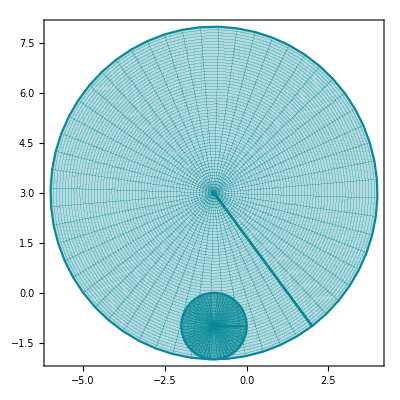

```mathematica
f[z_]=z*(3-4 I)+6+2 I;
g[r_,t_]=ComplexExpand[f[r Exp[I t]-1-I]];
p1=ParametricPlot[{r Cos[t]-1,r Sin[t]-1},{r,0,1},{t,0,2 Pi}];
p2=ParametricPlot[{Re[g[r,t]],Im[g[r,t]]},{r,0,1},{t,0,2 Pi},AxesOrigin->{0,0}];
Show[p1,p2,PlotRange->{{-6,4},{-2,8}}]
```

05

PLOTTING IMAGE OF RIGHT HALF PLANE UNDER LINEAR TRANSFORMATION

## Q)Show that image of right half plane Re z = x > 1under linear transformation w = (-1 + i)z -2 +3i is the half plane v> u+ 7 where u is Re w and v is Im w. Plot the map.

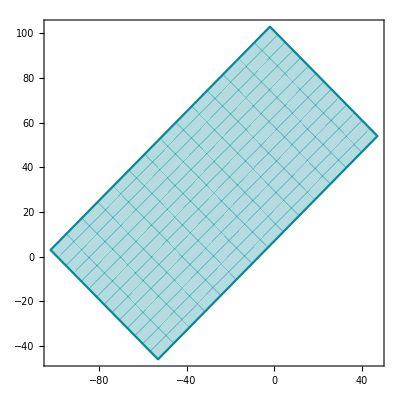

```mathematica
f[z_]=(-1+I)*z-2+3*I;
ParametricPlot[{Re[f[x+I y]],Im[f[x+I y]]},{x,1,50},{y,-50,50}]
```

06

PLOTTING IMAGE OF RIGHT HALF PLANE UNDER MAPPING

## Q)Show that image of right half plane A={z:Re z ≥ 1/2} under the mapping w=f(z)=1/z is the closed disk D_{1}(1)={w:|w-1| ≤1 in the w-plane

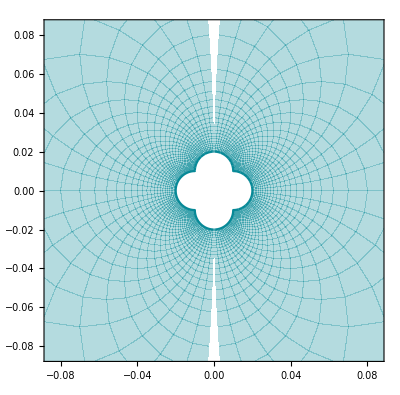

```mathematica
f[z_]=1/z;
ParametricPlot[{Re[f[x+I y]],Im[f[x+I y]]},{x,-50,50},{y,-50,50}]
```

07

PLOTTING PLOT OF THE GRID UNDER THE MAPPING

## Q) Make a plot of the vertical lines x = a for a = -1 , -1/2 , 1/2 , 1 and the horizontal lines y = b for b = -1 , -1/2 , 1/2 , 1 . Find the plot of this grid under the mapping w = 1/z .

i)Making the plot of the given horizontal and vertical lines

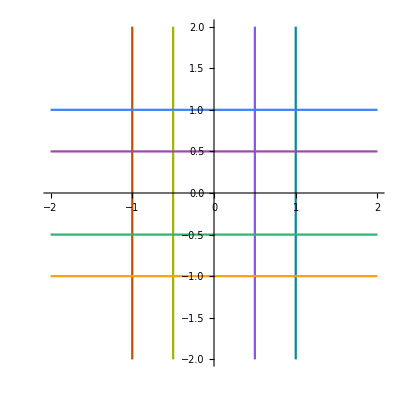

```mathematica
f[z_]=1/z;
p1=ParametricPlot[{{1,t},{-1,t},{1/2,t},{-1/2,t},{t,1},{t,-1},{t,1/2},{t,-1/2}},{t,-2,2}]
```

ii)Finding the image of the given plot under the mapping  w=1/z.

```mathematica
g[x_,y_]=1/(x+I*y);
u[x_,y_]=ComplexExpand[Re[g[x,y]]]
v[x_,y_]=ComplexExpand[Im[g[x,y]]]
```

x/(x^2+y^2)

-y/(x^2+y^2)

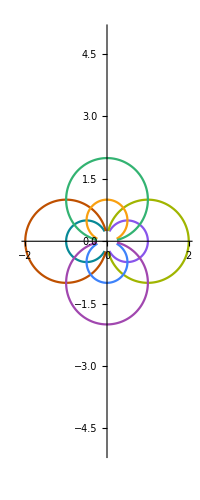

```mathematica
ParametricPlot[{{u[-1,t],v[-1,t]},{u[-1/2,t],v[-1/2,t]},{u[1,t],v[1,t]},{u[1/2,t],v[1/2,t]},{u[t,1],v[t,1]},{u[t,-1],v[t,-1]},{u[t,1/2],v[t,1/2]},{u[t,-1/2],v[t,-1/2]}},{t,-4,4},PlotRange->{{-2,2},{-5,5}}]
```

#Replacing t by 10t

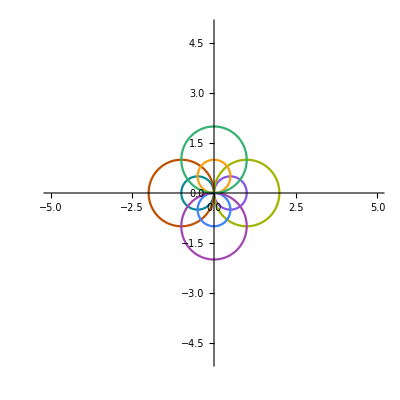

```mathematica
ParametricPlot[{{u[-1,10*t],v[-1,10*t]},{u[-1/2,10*t],v[-1/2,10*t]},{u[1,10*t],v[1,10*t]},{u[1/2,10*t],v[1/2,10*t]},{u[10*t,1],v[10*t,1]},{u[10*t,-1],v[10*t,-1]},{u[10*t,1/2],v[10*t,1/2]},{u[10*t,-1/2],v[10*t,-1/2]}},{t,-4,4},PlotRange->{{-5,5},{-5,5}}]
```

#Replacing t by 5t

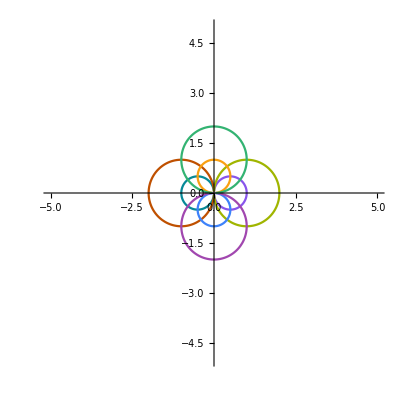

```mathematica
ParametricPlot[{{u[-1,5*t],v[-1,5*t]},{u[-1/2,5*t],v[-1/2,5*t]},{u[1,5*t],v[1,5*t]},{u[1/2,5*t],v[1/2,5*t]},{u[5*t,1],v[5*t,1]},{u[5*t,-1],v[5*t,-1]},{u[5*t,1/2],v[5*t,1/2]},{u[5*t,-1/2],v[5*t,-1/2]}},{t,-4,4},PlotRange->{{-5,5},{-5,5}}]
```

08

PARAMETRIC PLOT

## Q) Find a parametrization of the polygonal path C= C_1+C_2+C_3 fron -1+i to 3-i, where C_1 is the line from : -1+i to -1 , C_2 is the line from : -1 to 1+i and C_3 is the line from 1+i to 3-i. Make a plot of this path.

```mathematica
A=-1;
B=1+I;
L=A+(B-A)*t
```

-1+(2+ⅈ) t

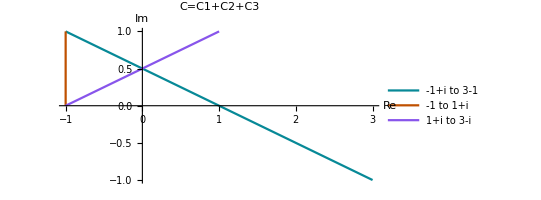

```mathematica
C1={-1+4t,1-2*t};
C2={-1,1-t};
C3={-1+2*t,t};
ParametricPlot[{C1,C2,C3},{t,0,1},PlotLabel->"C=C1+C2+C3",AxesLabel->{"Re","Im"},PlotLegends->{"-1+i to 3-1","-1 to 1+i","1+i to 3-i"}]
```

## Q)Integrate f(z) = (z+2)/z along the contour C , where a) C is the semicircle z = 2 e^it, 0≤t≤π b) C is the semicircle z= 2 e^it , Π≤t≤2π Also draw the curve C

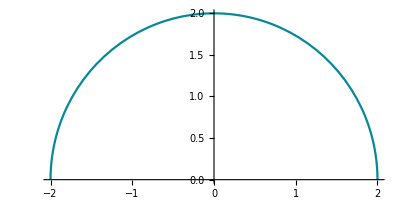

-4+2 ⅈ π

```mathematica
z[t_]=2*Exp[I*t];
f[z_]=(z+2)/z;
ParametricPlot[{2*Cos[t],2*Sin[t]},{t,0,Pi}]
Integrate[(f[z[t]])*(z'[t]),{t,0,Pi}]
```

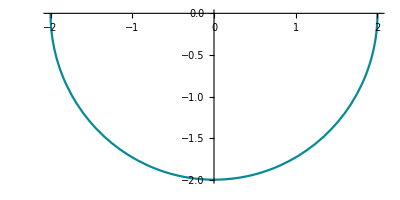

-2 ⅈ π+4 ⅈ Π+4 Cos[Π] (Cos[Π]+ⅈ Sin[Π])

```mathematica
f[z_]=(z+2)/z;ParametricPlot[{2*Cos[t],2*Sin[t]},{t,Pi,2*Pi}]
Integrate[(f[z[t]])*(z'[t]),{t,π,2*Π}]
```

## Q) Evaluate contour integral ∫c z ⅆz where c is the right hand half of the circle |z| = 2 from -2i to 2i . Also Plot C .

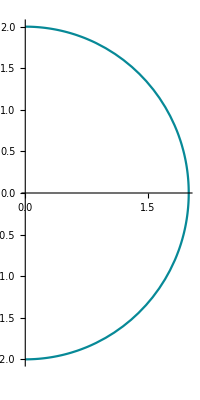

4 ⅈ π

```mathematica
z[t_]=2*Exp[I*t];
f[z_]=Conjugate[z];
ParametricPlot[{2*Cos[t],2*Sin[t]},{t,-Pi/2,Pi/2}]
Integrate[(f[z[t]])*(z'[t]),{t,-Pi/2,Pi/2}]
```

## Q) Plot the semicircle C with radius 1 centered at z = 2 and evaluate the contour integral of ∫c 1/(z-2) ⅆz.

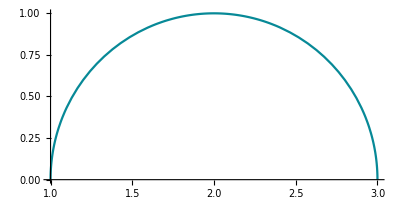

ⅈ π

```mathematica
z[t_]=2+Exp[I*t];
f[z_]=1/(z-2);
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,Pi}]
Integrate[(f[z[t]])*(z'[t]),{t,0,Pi}]
```

09

CALCULATING ∫e^z along a line segment L

## Q1) Plot the line segment ‘L’ joining the point A = 0 to B=2+π/4i and give an exact calculation of ∫_L^□ e^z ⅆz.

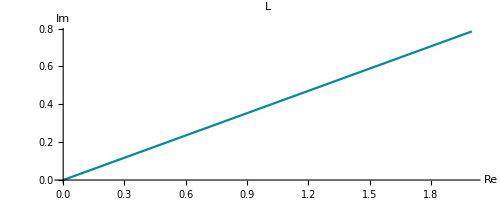

```mathematica
ParametricPlot[{2*t,(Pi/4)*t},{t,0,1},AxesLabel->{"Re","Im"},PlotLabel->"L"]
```

```mathematica
f[z_]:=Exp[z]
g[t_]:=(2+(Pi/4)*I)*t
Integrate[f[g[t]]*g'[t],{t,0,1}]
```

-1+(-1)^(1/4) ⅇ^2

## Q2) Plot the line segment ‘L’ joining the point A = 0 to B=2+π/2i and give an exact calculation of ∫_L^□ e^z ⅆz.

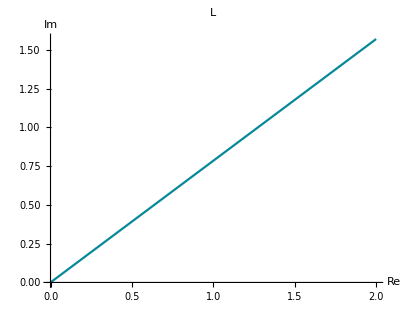

```mathematica
ParametricPlot[{2*t,(Pi/2)*t},{t,0,1},AxesLabel->{"Re","Im"},PlotLabel->"L"]
```

```mathematica
f[z_]:=Exp[z]
g[t_]:=(2+(Pi/2)*I)*t
Integrate[f[g[t]]*g'[t],{t,0,1}]
```

-1+ⅈ ⅇ^2

## Q3) Plot the line segment ‘L’ joining the point A =-1 to B=i and give an exact calculation of ∫_L^□ e^-z ⅆz.

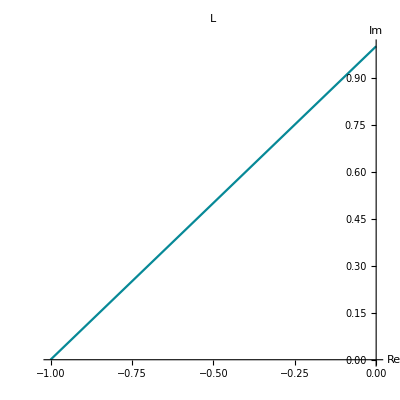

```mathematica
ParametricPlot[{t-1,t},{t,0,1},AxesLabel->{"Re","Im"},PlotLabel->"L"]
```

```mathematica
f[z_]:=Exp[-z]
g[t_]:=t-1+I*t
Integrate[f[g[t]]*g'[t],{t,0,1}]
```

-ⅇ^-ⅈ+ⅇ

## Q4) Plot the line segment ‘L’ joining the point A =-1+i to B=3+2i and give an exact calculation of ∫_L^□ e^-z ⅆz.

ClearAll

-1+ⅈ

3+2 ⅈ

(-1+ⅈ)+(4+ⅈ) t

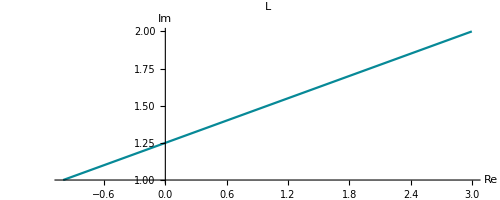

```mathematica
ClearAll
A=-1+I
B=3+2*I
L=A+(B-A)*t
Q[t_]:= L;
ParametricPlot[{Re[Q[t]],Im[Q[t]]},{t,0,1},AxesLabel->{"Re","Im"},PlotLabel->"L"]
```

10

EVALUATING DIFFERENT INTEGRALS along Semi circle

## Q) Plot the semicircle ‘C’ with radius 1 centered at z = 2 and evaluate the integral ∫_C^□ 1/(z-2)ⅆz

```mathematica
ParametricPlot[{2+Cos[t],Sin[t]},{t,0,Pi}]
```

-Graphics-

```mathematica
z[t_]:= 2+Cos[t]+I*Sin[t]
Integrate[1/(z[t]-2)*z'[t],{t,0,Pi}]
```

ⅈ π

Q2) Evaluate the integral  ∫ x^2 + i * y^2 𝕕𝕫 ‚z along the curve C where C is given by z(t) = t^2+ i*t , 0<=t<=1 .

```mathematica
h[t_]:=t^4+I*t^2
k[t_]:=t^2+I*t
Integrate[h[t]*k'[t],{t,0,1}]
```

(7 ⅈ)/10

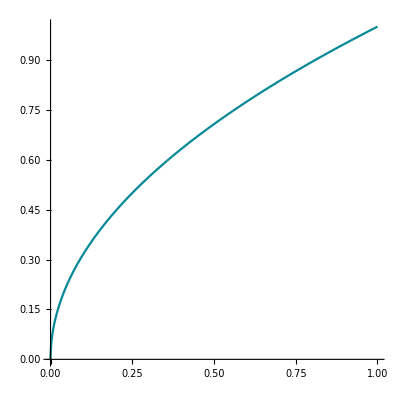

```mathematica
ParametricPlot[{t^2,t},{t,0,1}]
```

Q3) Evaluate the integral f(z)=1/z ‚z along the curve C where C is given by z(t) = RCos[t]+i Sin[t] , 0<=t<=2Pi , R is not equal to zero.

```mathematica
g[t_]:=R*Cos[t]+I*R*Sin[t]
j[t_]:=1/g[t]
Integrate[j[t]*g'[t],{t,0,2*Pi}]
```

2 ⅈ π

```mathematica
Manipulate[ParametricPlot[{R*Cos[t],R*Sin[t]},{t,0,2*Pi}],{R,1,10,2}]
```

Q4)  Evaluate the integral for f(z) = z^2 , along c_1 , c_2 and c_3 contour and show that integral evaluated along contour c_1is equal to sum of integral evaluated along c_2 and c_3 .
c_1: line passing through origin , t + It
c_2: imaginary axis , It
c_3: line t + It

```mathematica
z1[t_]:=t+I*t
h1=Integrate[z1[t]^2*z1'[t],{t,0,1}]
```

-2/3+(2 ⅈ)/3

```mathematica
z2[t_]:=I*t
h2=Integrate[z2[t]^2*z2'[t],{t,0,1}]
```

-ⅈ/3

```mathematica
z3[t_]:=I+t
h3=Integrate[z3[t]^2*z3'[t],{t,0,1}]
```

-2/3+ⅈ

```mathematica
h1==h2+h3
```

True

Observation : here we can see that integration evaluated along c_1 is equal to the sum of integration evaluated along c_2 and c_3 .

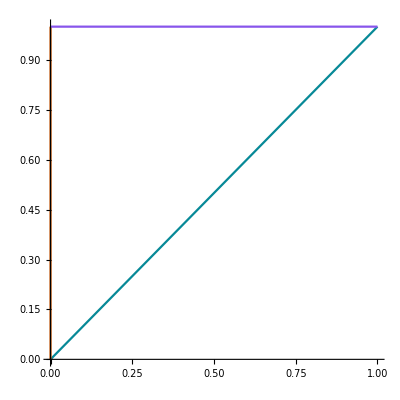

```mathematica
ParametricPlot[{{Re[z1[t]],Im[z1[t]]},{Re[z2[t]],Im[z2[t]]},{Re[z3[t]],Im[z3[t]]}},{t,0,1}]
```

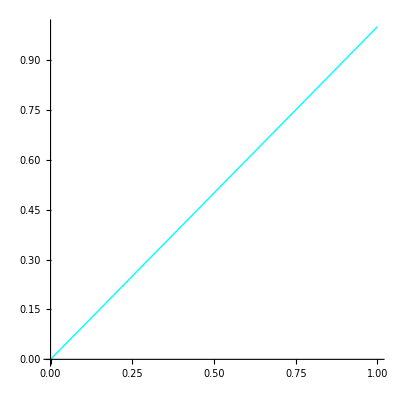

```mathematica
c1={t,t};
ParametricPlot[c1,{t,0,1},PlotStyle->{Cyan,Thick}]
```

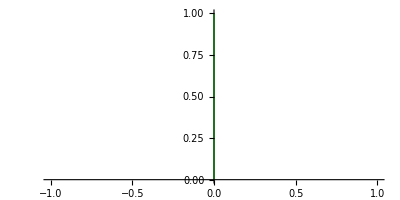

```mathematica
c2={0,t};
ParametricPlot[c2,{t,0,1},PlotStyle->{Green,Thick}]
```

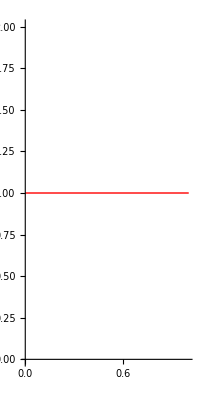

```mathematica
c3={t,1};
ParametricPlot[c3,{t,0,1},PlotStyle->{Red,Thick}]
```

Observation : Here we have plotted contours c_1, c_2 and c_3.

11

CONTOUR

## Q1) Show that ∫_c1^□ zⅆz =∫_c2^□ zⅆz = 4+2i , where c_1 is the line segment from -1-i to 3 + i and c_2 is the portion of the parabola x = y^2 + 2y joining -1-i to 3+i .Make plot of Contour c_1 and c_2 joining -1-i to 3+i.

```mathematica
b[t_]:=(4*t-1)+I*(2*t-1)
Integrate[b[t]*b'[t],{t,0,1}]
```

4+2 ⅈ

```mathematica
b1[t_]:=(t^2+2*t)+I*t
Integrate[b1[t]*b1'[t],{t,-1,1}]
```

4+2 ⅈ

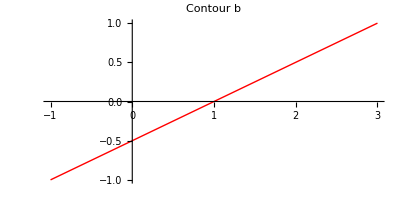

```mathematica
p1=ParametricPlot[{4*t-1,2*t-1},{t,0,1},PlotStyle->{Red,Thick},PlotLabel->"Contour b"]
```

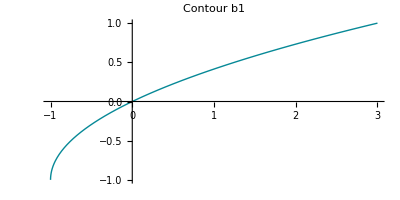

```mathematica
p2=ParametricPlot[{t^2+2*t,t},{t,-1,1},PlotStyle->{Mangenta,Thick},PlotLabel->"Contour b1"]
```

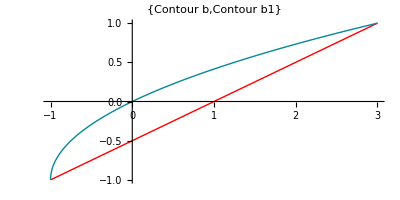

```mathematica
Show[p1,p2,PlotLabel-> {"Contour b","Contour b1"}]
```

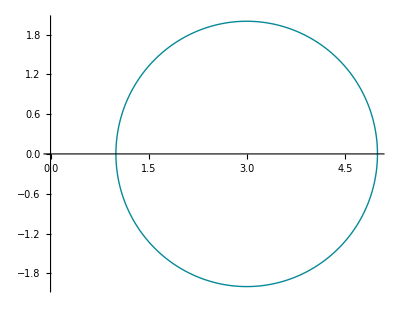

```mathematica
p2=ParametricPlot[{3+2*Cos[t],2*Sin[t]},{t,0,2*Pi},PlotStyle->{Mangenta,Thick},AxesOrigin->{0,0}]
```

## Q2) Plot the circle with radius 2 and center z=3 and evaluate the integral along the contour C ∫_C^□ 1/(z-1)ⅆz and ∫_C^□ 1/(z(z-1))ⅆz .

```mathematica
s[t_]:=3+2*Cos[t]+I*2*Sin[t]
I1=Integrate[1/(s[t]-1)*s'[t],{t,0,2Pi}]
```

Integrate::idiv: Integral of (ⅈ Cos[t]-Sin[t])/(1+Cos[t]+ⅈ Sin[t]) does not converge on {0,2 π}.

∫_0^(2 π) (2 ⅈ Cos[t]-2 Sin[t])/(2+2 Cos[t]+2 ⅈ Sin[t])ⅆt

```mathematica
I1=Integrate[1/(s[t]*(s[t]-1))*s'[t],{t,0,2Pi}]
```

Integrate::idiv: Integral of -Sec[t/2]^2/(2 (5 ⅈ+Tan[t/2])) does not converge on {0,2 π}.

∫_0^(2 π) (2 ⅈ Cos[t]-2 Sin[t])/((2+2 Cos[t]+2 ⅈ Sin[t]) (3+2 Cos[t]+2 ⅈ Sin[t]))ⅆt

OBSERVATION : We are getting an error while evaluating the Integral because the function f(z) has a point of singularity i.e. 1 at t = π , therefore the given function is not continuous in the given Domain .

## Q3) Plot a line passing through -1-i to 1+i and evaluate the integral along the contour C,∫_C^□ 1/(z-1)ⅆz and ∫_C^□ 1/(z(z-1))ⅆz .

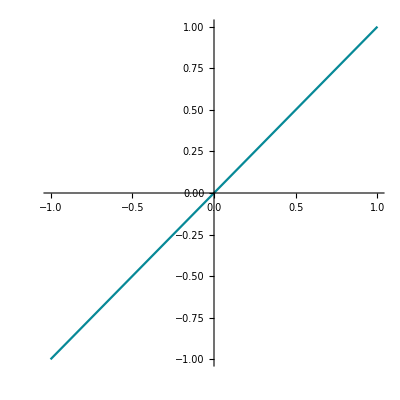

```mathematica
ParametricPlot[{2*t-1,2*t-1},{t,0,1}]
```

```mathematica
s[t_]:=(2*t-1)+I*(2*t-1)
Integrate[1/(s[t]-1)*s'[t],{t,0,1}]
```

-1/2 ⅈ (π+2 ArcTan[1/2]-ⅈ Log[5])

```mathematica
s[t_]:=(2*t-1)+I*(2*t-1)
N[Integrate[1/(s[t]-1)*s'[t],{t,0,1}]]
```

-0.804719-2.03444 ⅈ

```mathematica
s[t_]:=(2*t-1)+I*(2*t-1)
Integrate[1/(s[t]*(s[t]-1))*s'[t],{t,0,1}]
```

Integrate::idiv: Integral of 2/((2+ⅈ)-(6+4 ⅈ) t+(4+4 ⅈ) t^2) does not converge on {0,1}.

∫_0^1 (2+2 ⅈ)/((-2+2 t+ⅈ (-1+2 t)) (-1+2 t+ⅈ (-1+2 t)))ⅆt

OBSERVATION : We are getting an error while evaluating the Integral because the function f(z) has a point of singularity i.e. 1 and 0 , therefore the given function is not continuous in the given Domain .

12

ML INEQUALITY

## Use ML inequality to show absolute value of integral |1/(z^2+1)|≤ 1/(2√5) where C is the straight line segment from 2 to 2+i. While solving represent the distance from the point ‘z’ to the points ‘i’ & ‘-i’ respectively, i.e. |z-i| and |z+i| on the complex plane ℂ.

```mathematica
A=2;
B=2+I;
g[t_]:=A+(B-A)*t;
f[z_]:=1/(z^2+1)
V=N[Abs[Integrate[f[g[t]]*g'[t],{t,0,1}]]]
V<=1/(2*Sqrt[5])
```

0.187249

True

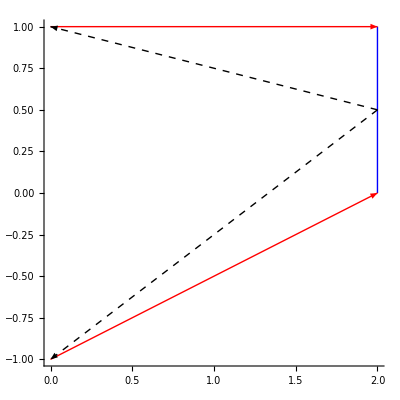

```mathematica
z=2+I/2;
Show[Graphics[{Blue,Thick,Line[{{2,0},{2,1}}]}],
Graphics[{Red,Arrow[{{0,1},{2,1}}]}],
Graphics[{Red,Arrow[{{0,-1},{2,0}}]}],
Graphics[{Dashed,Arrow[{{2,0.5},{0,1}}]}],
Graphics[{Dashed,Arrow[{{2,0.5},{0,-1}}]}],Axes->True]
```

Hence verified using ML inequality where M=1/2√ 5 and L=1.

13

LAURENT SERIES

## Find and plot three different Laurent Series representations for the function f(z)=3/(2+z-z^2), involving powers of z.

```mathematica
Grid[Table[{n,Normal[Series[3/(2+w-w^2),{w,n,10}]]},{n,{0,2,Infinity}}],Frame->All]
```

0 | 3/2-(3 w)/4+(9 w^2)/8-(15 w^3)/16+(33 w^4)/32-(63 w^5)/64+(129 w^6)/128-(255 w^7)/256+(513 w^8)/512-(1023 w^9)/1024+(2049 w^10)/2048
2 | 1/3+(2-w)/9-1/(-2+w)+1/27 (-2+w)^2-1/81 (-2+w)^3+1/243 (-2+w)^4-1/729 (-2+w)^5+(-2+w)^6/2187-(-2+w)^7/6561+(-2+w)^8/19683-(-2+w)^9/59049+(-2+w)^10/177147
∞ | -513/w^10-255/w^9-129/w^8-63/w^7-33/w^6-15/w^5-9/w^4-3/w^3-3/w^2

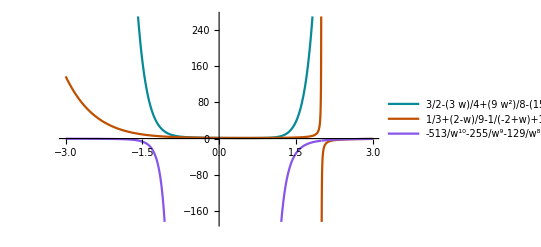

```mathematica
Plot[Evaluate[Table[{Normal[Series[3/(2+w-w^2),{w,n,10}]]},{n,{0,2,Infinity}}]],{w,-3,3},PlotLegends->"Expressions"]
```

14

LOCATE THE POLES

## Locate the poles of f(z)=1/(5 z^4+26 z^2+5) and specify their order

```mathematica
q[t_]:=1/(5*t^4+26*t^2+5)
Print["q(t)=",q[t]]
solset=Sort[Solve[Denominator[f[t]]==0,t]];
S={t/.solset[[1]],t/.solset[[2]],t/.solset[[3]],z/.solset[[4]]};
Print["The singularities are:",S]
```

q(t)=1/(5+26 t^2+5 t^4)

The singularities are:{-ⅈ/(√5),ⅈ/(√5),-ⅈ √5,2+ⅈ/2}

We can see that there are no repeated roots, thus all poles are of order 1.

15

LOCATE THE ZEROES AND POLES

## Locate the zeros and poles of g(z)=(π cot(πz))/Z^2 and determine their order. Also justify that Res (g, 0) = π^2/3

```mathematica
q[z_]:=(Pi Cot[Pi z])/(z^2);
Reduce[q[z]==0,z]
```

C[1]∈ℤ&&z≠0&&z==(π/2+π C[1])/π

by replacing c1 with any integer in the above expr we get zero for g(z)

```mathematica
pole=Solve[Denominator[q[z]]==0,z]
```

{{z→0},{z→0}}

here we have pole at 0 with 2

```mathematica
Residue[q[z],{z,0}]
```

-π^2/3

16

LOCATE THE ZEROES AND POLES

## Evaluate the integral of exp(2/z) over c1+(0) denoting the circle {z:| z | =1} with positive orientation . Similarly evaluate the integral of 1/(z^4+z^3-2 z^2).

```mathematica
g[t_]:= Cos[t]+ I*Sin[t];
f[z_]:= Exp[2/z]
Integrate[f[g[t]]*g'[t],{t,0,2*Pi}]
```

4 ⅈ π

```mathematica
h[z_]:=1/(z^4+z^3-2*z^2)
Integrate[h[g[t]]*g'[t],{t,0,2*Pi}]
```

Integrate::idiv: Integral of -(ⅈ Cos[2 t])/(-1+Cos[t]-3 ⅈ Sin[t])-Sin[2 t]/(-1+Cos[t]-3 ⅈ Sin[t]) does not converge on {0,2 π}.

∫_0^(2 π) (ⅈ Cos[t]-Sin[t])/(-2 (Cos[t]+ⅈ Sin[t])^2+(Cos[t]+ⅈ Sin[t])^3+(Cos[t]+ⅈ Sin[t])^4)ⅆt